```mathematica
<<"/home/josu/PRM/RRT/RandomData.m"
```

## Punto 2: generar una distribución uniforme

```mathematica
muestras=10000;
listaUnifor=Table[RandomData[],{i,muestras}];
```

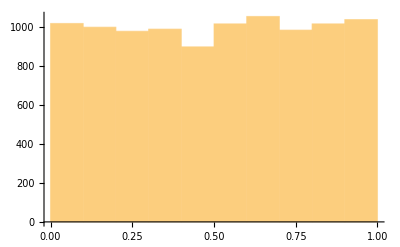

```mathematica
Histogram[listaUnifor,10]
```

```mathematica
lamda=80;
mu=100;
ro=lamda/mu;
```

## Punto 3 : el generador de numeros aleatorios basado en el metodo de transformación inversa se implementa en RandomExp

```mathematica
InterArrivalsTime=Table[RandomExp[lamda],muestras];
```

InterArrivalsTime lo que calcula realmente es que espacio de tiempo hay entre las llegadas de los paquetes que es exponencial lo que se demuestra en el siguiente histograma

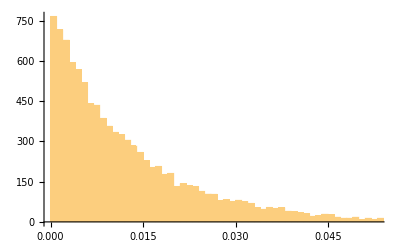

```mathematica
Histogram[InterArrivalsTime,100]
```

```mathematica
ArrivalsTimes = Accumulate[InterArrivalsTime];
```

Acumulas para saber en que tiempo aboslutos estan llegando los paquetes, es decir cada valor es el momento en el que llega un paquete

```mathematica
ServTime=Table[RandomExp[mu],muestras];
```

```mathematica
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
Map[(If[checkTime>=#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&,arrivals]]
```

Aqui se le pasa los tiempos absolutos de llegada y cuanto tiempo tardan en servirse. Checktime es cuando termina de servir un paquete n. Entonces empieza con n=1, primer paquete, e inicializa al tiempo de llegada del primer paquete porque cunado llega el primero esta libre, entonces en el If sale que si se cumple y por tanto el siguiente checktime es el checktime actual mas lo que tarde en servir. El If compara si cuando el paquete llega se esta libre o no, si se esta libre el siguiente momento en el que te quedas libre es el tiempo de llegada más el tiempo que tardas en servir el paquete; sino es el tiempo en el que te has quedado libre (más tarde de que el paquete llegue) más el tiempo que tardes en servirlo. Esto devuelve los tiempos en los que se sirven los paquetes

```mathematica
Departu=FifoSchedulling[ArrivalsTimes,ServTime];
```

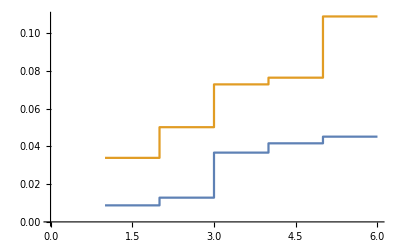

```mathematica
ListStepPlot[{ArrivalsTimes[[1;;5]],Departu[[1;;5]]}]
```

```mathematica
Manipulate[ListStepPlot[{ArrivalsTimes[[origin;;origin+width]],Departu[[origin;;origin+width]]}],{origin,1,1000-width,1},{width,10,50,1}]
```

Aqui ya se podría ver cual es el número de usuarios que hay en cada instante de tiempo haciendo la resta entre las dos funciones, sin embagro, es mucho más facil de ver en el siguiente apartado

## Punto 4 : calcular el numero de usarios y el cambio que sufren en cada instante de tiempo

```mathematica
NumUsers[arrivals_,departures_]:=
Module[{i,j,users,usuarios},
usuarios={0,0};
For[i=1;j=1;users=0,
i<Length[arrivals]&&j<Length[departures],
If[
arrivals[[i]]≤departures[[j]],
usuarios=Join[usuarios,{arrivals[[i]]},{users}];users++;usuarios=Join[usuarios,{arrivals[[i]]},{users}];i++,
usuarios=Join[usuarios,{departures[[j]]},{users}];users--;usuarios=Join[usuarios,{departures[[j]]},{users}];j++;];
];
Return[Partition[usuarios,2]];
]
```

Esta funcion lo que hace es a partir de los tiempo de llegada y de salida calcular cuantos usuarios hay, recorre los 2 arrays con diferentes indices que solo se incrementan al suceder una llegada o una salida y a su vez se suma 1 o resta 1 a una variable que representa el numero de usuarios en cada momento. Además del numero de usuarios en la lista se devuelve el tiempo en el que sucede la llegada o salida para poder así representarlo.

```mathematica
usuarios=NumUsers[ArrivalsTimes,Departu];
```

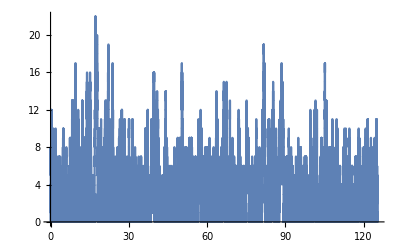

```mathematica
ListLinePlot[usuarios]
```

```mathematica
Manipulate[ListLinePlot[usuarios[[origin;;origin+width]]],{origin,1,Length[usuarios]-width,1},{width,10,50,1}]
```

## Punto 5: Comparar la curva de valor medio teorica con la practica

Teorico

```mathematica
a=Plot[1/(1-ro),{ro,0,1},AxesOrigin->{0,0}];
```

Simulado

Se calcula primero cual sería el tiempo medio de espera para una lamda y un mu concretos, simplemente calulcando cuanto tiempo esta cada paquete y acumulando todos los retardos para luego dividirlo entre el numero de muestras.

```mathematica
TiempEsperaMedio[lamda_,mu_,numMuestras_]:=
Module[{n,acum,tiempoMed},
acum=0;
InterArrivalTime=Table[RandomExp[lamda],numMuestras];
ServiceTime=Table[RandomExp[mu],numMuestras];
ArrivalsTime=Accumulate[InterArrivalTime];
DepartureTime=FifoSchedulling[ArrivalsTime,ServiceTime];
For[n=1,
n≤numMuestras,
n++,
acum=acum+DepartureTime[[n]]-ArrivalsTime[[n]];
];
tiempoMed=acum/numMuestras;
Return[tiempoMed];
]
```

A partir de la función que permite calcular el tiempo de espera medio simplemente se realiza este calculo para diferentes valores de lamda con un mu fijo para poder así ver el efecto de la variación de lamda.

```mathematica
CalculoTiempoMedio[]:=
Module[{mu,lamda,tiempo,array,ro},
mu=100;
array={};
For[lamda=2,lamda≤100,lamda=lamda+4,
ro=N[lamda/mu];
tiempo=TiempEsperaMedio[lamda,mu,10000];
array=Join[array,{ro},{tiempo*mu}];
];
Return[Partition[array,2]]
]
```

```mathematica
b=ListPlot[CalculoTiempoMedio[]];
```

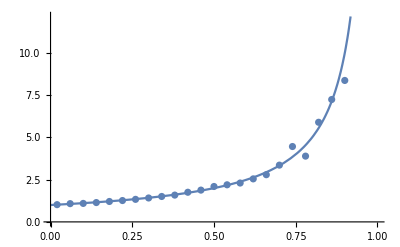

```mathematica
Show[a,b]
```

## Punto 6: Probabilidades de estados en 3 formas -> teórico, simulado y en base a la propiedad PASTA

Teorico

```mathematica
ProbabilidadTeorica[lamda_,mu_]:=
Module[{ro,probabilidad,probEstadosTeo,i},
probEstadosTeo={};
ro=lamda/mu;
For[i=0,
i<30,
i++,
probabilidad=(1-ro)*(ro^i);
probEstadosTeo=Join[probEstadosTeo,{probabilidad}];
];
Return[probEstadosTeo];
]
```

```mathematica
probTeo=ProbabilidadTeorica[80,100]//N;
```

Simulado

A partir de la lista de numero de usuarios y en que tiempo suceden los cambios se van acumulando los tiempos en los que el sistema se encuentra en un estado concreto (un número de usuarios) y luego se divide ese tiempo entre el tiempo total.

```mathematica
ProbabilidadSimulada[usuarios_]:=
Module[{proEstados,tiempo,n,i,acum,prob},
tiempo=usuarios[[Length[usuarios]]][[1]];
proEstados={};
For[n=0,
n<30,
n++,
acum=0;
For[i=1,
i<Length[usuarios]-1,
i++,
If[usuarios[[i]][[2]]==n&&usuarios[[i+1]][[2]]==n,acum=acum+usuarios[[i+1]][[1]]-usuarios[[i]][[1]]];
];
prob=acum/tiempo;
proEstados=Join[proEstados,{prob}];
];
Return[proEstados]
]
```

```mathematica
probSimu=ProbabilidadSimulada[usuarios];
```

PASTA

```mathematica
NumUsersArrival[arrivals_,departures_]:=
Module[{i,j,users,usuarios},
usuarios={0,0};
For[i=1;j=1;users=0,
i<Length[arrivals]&&j<Length[departures],
If[
arrivals[[i]]≤departures[[j]],
usuarios=Join[usuarios,{users}];users++;i++,
users--;j++;];
];
Return[usuarios];
]
```

Para calcular la probabilidad partiendo de la propiedad PASTA lo que hacemos es fijarnos solo en las llegadas y mirar justo en el instante anterior cuantos usuarios habia y luego dividir cuantas veces hemos encontrado que estaba en un estado entre el numero total de veces que hemos muestreado, y según la propiedad PASTA el resultado se debe ajustar de forma bastante precisa a la realidad, tal y como se demuestra a continuación.

```mathematica
ProbabilidadPASTA[usuarios_]:=
Module[{n,i,proEstados,prob,acum},
proEstados={};
For[n=0,
n<30,
n++,
acum=0;
For[i=1,
i<Length[usuarios],
i++,
If[usuarios[[i]]==n,acum++];
];
prob=acum/N[Length[usuarios]];
proEstados=Join[proEstados,{prob}];
];
Return[proEstados]
]
```

```mathematica
lamda=80;
mu=100;
muestras=10000;
InterArrivalsTime=Table[RandomExp[lamda],muestras];
ArrivalsTime = Accumulate[InterArrivalsTime];
ServTime=Table[RandomExp[mu],muestras];
Departu=FifoSchedulling[ArrivalsTime,ServTime];
usuariosArrival=NumUsersArrival[ArrivalsTime,Departu];
```

```mathematica
probPASTA=ProbabilidadPASTA[usuariosArrival];
```

```mathematica
CrearLista[prob_]:=
Module[{i,lista},
lista={};
For[i=1,
i≤Length[prob],
i++,
lista=Join[lista,{i-1,prob[[i]]}];
];
Return[Partition[lista,2]]
]
```

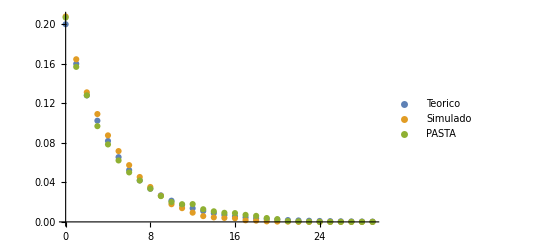

```mathematica
ListaProbTeo=CrearLista[probTeo];
ListaProbSimu=CrearLista[probSimu];
ListaProbPASTA=CrearLista[probPASTA];
ListPlot[{ListaProbTeo,ListaProbSimu,ListaProbPASTA},PlotLegends->{"Teorico","Simulado","PASTA"}]
```

En este caso se ve claro como los diferentes resultados son muy similares, es decir, la simulacion realizada es correcta y ademas es visible que la propiedad PASTA se cumple

## Punto 7: Rendimiento de colas

## M/M/2

En primera instancia el modelo M/M/2 empieza como el M/M/1 porque le mecanismo de llegadas es el mismo, es decir se puede calcular igual; sin embargo para las salida los tiempos de servicio siguen una distribución diferente en el caso en el que se esta con un paquete y cuando se está con mas de uno ya sea tratandolos o en espera. La idea que yo planteo es generar un array de checktime donde se van guardando los tiempos de salida, de forma que no solo se sepa el ultimo tiempo de salida sino que comparando los indice de ambos arrays se pueda saber si el utlimo paquete que ha salido era justo el anterior y por tanto la cola está vacia o no para aplicar un tiempo de servicio de mu o de 2*mu. Para realizarlo he hecho la simplificación de es una única cola de salida que sirve con tiempo “mu” si hay un solo usuario o “2*mu” si hay mas de un usuario.

```mathematica
lamda=80;
numMuestras=1000;
mu=100;
<<"/home/josu/PRM/RRT/RandomData.m"
```

```mathematica
InterArrivalsTime=Table[RandomExp[lamda],numMuestras];
ArrivalsTimes = Accumulate[InterArrivalsTime];
ServiceTimeMu=Table[RandomExp[mu],numMuestras];
ServiceTime2Mu=Table[RandomExp[2*mu],numMuestras];
```

```mathematica
DeparturesMM2[arrivals_]:=
Module[{i,j,users,checkTime},
checkTime={};
users=0;
checkTime=Join[checkTime,{arrivals[[1]]+RandomExp[mu]}];
For[i=1;j=1;users=0,
i<Length[arrivals],
If[checkTime[[j]]<= arrivals[[i]],
users--;j++;
If[j==i,checkTime=Join[checkTime,{arrivals[[i]]+RandomExp[mu]}]],
If[j!=i,checkTime=Join[checkTime,{checkTime[[j]]+RandomExp[2*mu]}]];
users++;i++;]
];
Return[checkTime];
]
```

```mathematica
Departures=DeparturesMM2[ArrivalsTimes];
```

```mathematica
DeparturesOrdered=Sort[Departures];
```

```mathematica
usuariosMM2=NumUsers[ArrivalsTimes,DeparturesOrdered];
```

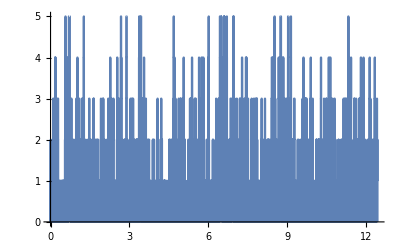

```mathematica
ListLinePlot[usuariosMM2]
```

```mathematica
Manipulate[ListLinePlot[usuariosMM2[[origin;;origin+width]]],{origin,1,Length[usuariosMM2]-width,1},{width,10,50,1}]
```

Se puede apreciar como ahora que nos encontramos en un modelo con 2 colas el número máximo de usuarios que llega a encontrar en el sistema esta en torno a los 7 usuarios mientras que para el mismo valor de mu y lamda en el caso de M/M/1 había momentos en los que llegabamos a encontrar hasta 20 usuarios; esta simulación demuestra que una cola M/M/2 sirve a los usuarios más rápido que una cola M/M/1.

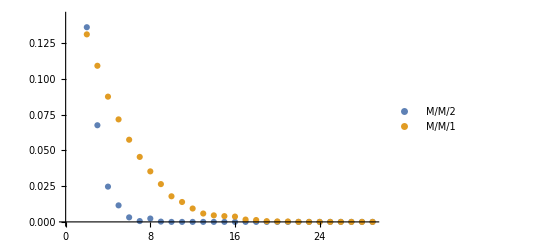

```mathematica
probSimuMM2=ProbabilidadSimulada[usuariosMM2];
ListaProbSimuMM2=CrearLista[probSimuMM2];
ListPlot[{ListaProbSimuMM2,ListaProbSimu},PlotLegends->{"M/M/2","M/M/1"}]
```

En este caso también vemos claramente como para el caso de M/M/2 las probabilidades son mayores para estados cercanos a 0 mientras que la probabilidad se hace menor para valores altos de usuarios esperando en cola.